# 4.3 Renyi dimension of Hénon map

#### a)

Initialise the parameters:

```mathematica
a = 1.4;
b = 0.3;
```

The Hénon map is given by:

```mathematica
henon[{x_,y_}] := {y+1-a*x^2, b*x}
```

We sample different initial conditions and plot them

```mathematica
z = 0.2;
```

```mathematica
dz = 2/150;
```

```mathematica
initialC = Tuples[{Range[-z,z,dz],Range[-z,z,dz]}];
```

```mathematica
list = Table[Drop[NestList[henon, {initialC[[i,1]],initialC[[i,2]]}, 200],100],{i,1,Length[initialC]}];
```

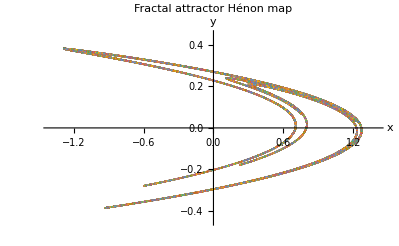

```mathematica
ListPlot[list,PlotLabel-> "Fractal attractor Hénon map" , AxesLabel->{"x","y"}, PlotRange->{{-1.4,1.4}, {-0.45,0.45}}]
```

Note that the structure above satisfies the properties of a strange attractor (bounded, aperiodic, structure on all scales, sensitive on initial conditions,...). It’s also somewhat clear that it’s dimension is larger than 1 (keeps repeating on all scales) and smaller than 2 (doesn’t fill whole plane) --> fractal dimension.

#### b)

```mathematica
data = {};
```

```mathematica
For[i = 1, i < Length[list], i++,
For[j = 1, j < Length[list[[1]]],j++,
data = Append[data,list[[i,j]]]
] ]
```

```mathematica
ϵ = Subdivide[10^-3, 5*10^-2,50]; (* bin size *)
```

```mathematica
lnI0 = Range[Length[ϵ]];
lnI1 = Range[Length[ϵ]];
lnI2 = Range[Length[ϵ]];
```

```mathematica
For[k=1,k<Length[ϵ]+1,k++,
bins=Normal[BinCounts[data,{-1.4,1.4,ϵ[[k]]},{-0.45,0.45,ϵ[[k]]}]//Flatten];
(* BinCounts tells us how many points there lie within a bin of size ϵ[[k]] together with the 'position' of the box on a grid. Since we only care about the amount and not about the position, Flatten can be used to remove the grid 'location'. Finally, because BinCounts outputs a sparse array, we convert it into a matrix using the Normal command. This makes it easier to remove the 0's in the next line: *);

bins=DeleteCases[bins,0|0]; (* 0's lead to problems down the line. Since they don't give a contribution to I_q, we can safely discard them here *)

Ntot = Total[bins];
bins = bins/Ntot; (* normalisation, so from now on bins represents the probability to be within a bin*);

lnI0⟦k⟧=(1-0)^-1*Log[Total[bins^0]]; (* calculate (1-q)^(-1)* Log[I_q] for q = 0*);
lnI1⟦k⟧=Total[-Log[bins]*bins]; (* use formula on p 10 for the case of q = 1*);
lnI2⟦k⟧=(1-2)^-1*Log[Total[bins^2]];

]
```

To show what this code does, we show a few iterations:

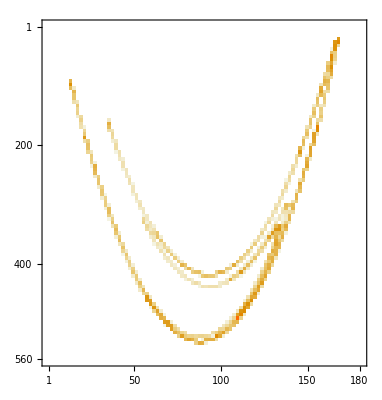

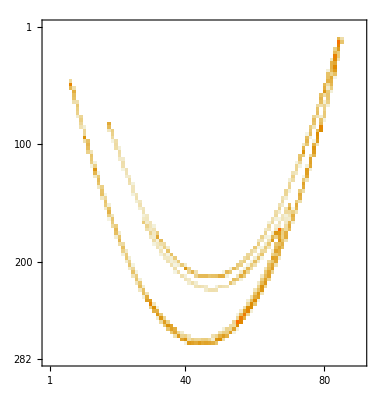

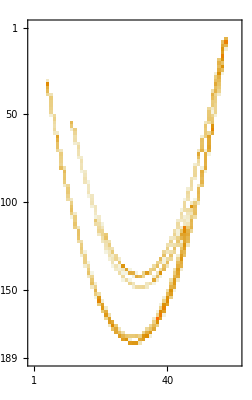

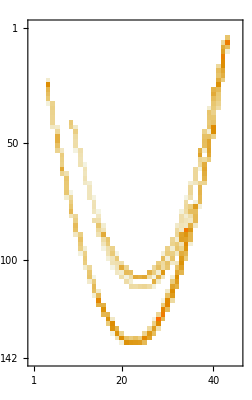

```mathematica
For[k=1,k<5,k++,
Print[MatrixPlot[BinCounts[data,{-1.4,1.4,ϵ[[k]]*5},{-0.45,0.45,ϵ[[k]]*5}]]]];
```

It’s clear that as ϵ increases (the bins become larger), the resolution of the figure decreases since more points are combined into the same bin.

```mathematica
plot0 = Transpose@{Log[1/ϵ],lnI0};
plot1= Transpose@{Log[1/ϵ],lnI1};
plot2 = Transpose@{Log[1/ϵ],lnI2};
```

```mathematica
p0=ListPlot[plot0, PlotStyle->Red,PlotLegends->{"q = 0"}];
```

```mathematica
p1 = ListPlot[plot1, PlotStyle->Green,PlotLegends->{"q = 1"}];
```

```mathematica
p2 = ListPlot[plot2, PlotStyle->Blue,PlotLegends->{"q = 2"}];
```

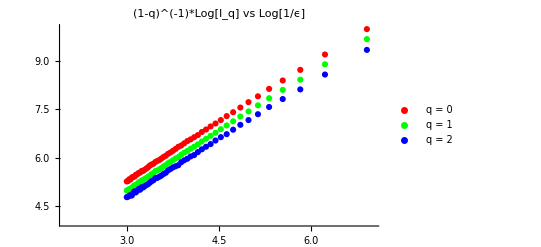

```mathematica
Show[p0,p1,p2, PlotRange->{{2,7}, {4,10}}, AxesOrigin->Automatic, PlotLabel->"(1-q)^(-1)*Log[Ι_(<q>)] vs Log[1/ϵ]"]
```

Note that (1-q)^(-1)*Log[Ι_q]follows a linear trend w.r.t.  Log[1/ϵ], where the slope is given by D_q.

```mathematica
line0 = Fit[plot0,{1,x},x]
```

1.63513+1.21855 x

```mathematica
line1 = Fit[plot1,{1,x},x]
```

1.34352+1.21829 x

```mathematica
line2 = Fit[plot2,{1,x},x]
```

1.22706+1.18723 x

```mathematica
l0 =Plot[line0, {x,2.5,7},PlotStyle->Black,PlotLegends->{"Fit q = 0"}];
```

```mathematica
l1 =Plot[line1, {x,2.5,7},PlotStyle->Cyan,PlotLegends->{"Fit q = 1"}];
```

```mathematica
l2 =Plot[line2, {x,2.5,7},PlotStyle->Yellow,PlotLegends->{"Fit q = 2"}];
```

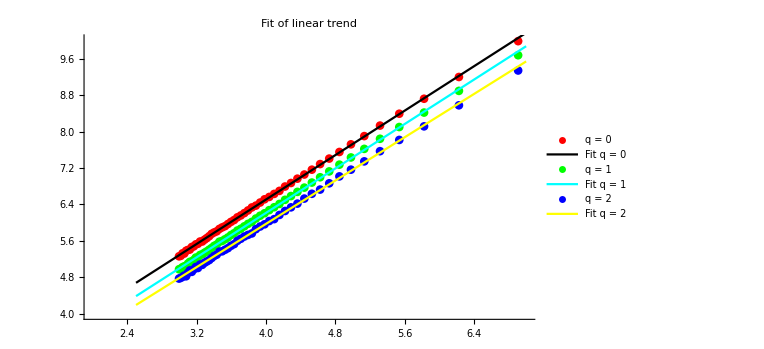

```mathematica
Show[p0,l0,p1,l1,p2,l2,PlotRange->{{2,7}, {4,10}}, AxesOrigin->Automatic,PlotLabel->"Fit of linear trend "]
```

Note that the linear fit indeed gives a very good approximation for all q, so we can indeed conclude that (1-q)^-1*Log[Ι_q]follows a linear trend w.r.t.  Log[1/ϵ]. 
The Renyi dimension is given by the slope of these fitted lines.

```mathematica
D0 = line0[[2,1]]
```

1.21855

```mathematica
D1= line1[[2,1]]
```

1.21829

```mathematica
D2 = line2[[2,1]]
```

1.18723

#### d)

We calculate D_q for multiple values of q with the same procedure as above

```mathematica
q = Subdivide[0,4,9]
```

{0,4/9,8/9,4/3,16/9,20/9,8/3,28/9,32/9,4}

```mathematica
Dq = Range[Length[q]];
```

```mathematica
For[j= 1,j<Length[Dq]+1,j++,
qj = q[[j]];
Id = Range[Length[ϵ]];
For[k=1,k<Length[ϵ]+1,k++,
bins=Normal[BinCounts[data,{-1.5,1.5,ϵ[[k]]},{-0.5,0.5,ϵ[[k]]}]//Flatten];

bins=DeleteCases[bins,0|0];

Ntot = Total[bins];
bins = bins/Ntot;

Id⟦k⟧=(1-qj)^-1*Log[Total[bins^qj]];

];
fitdata = Transpose@{Log[1/ϵ],Id};
l= Fit[fitdata,{1,x},x];
Dq[[j]] = l[[2,1]]
]
```

```mathematica
dataq = Transpose@{q,Dq}
```

{{0,1.21949},{4/9,1.22248},{8/9,1.21918},{4/3,1.2104},{16/9,1.19491},{20/9,1.1716},{8/3,1.14065},{28/9,1.10416},{32/9,1.0657},{4,1.02877}}

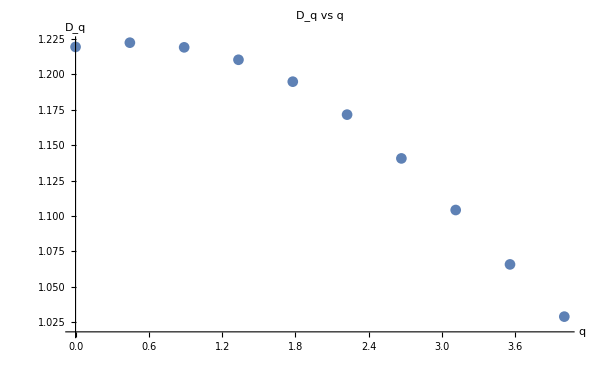

```mathematica
ListPlot[dataq, PlotLabel->"D_q vs q", AxesLabel->{"q","D_q"}]
```

It is clear that D_q is a non-increasing function of q. The initial increase for the second q value is very small (order 0.003) and is probably a numerical error. This error can most likely be eliminated by taking more points of the attractor.

#### e)

To calculate the Lyapunov exponents,  one needs a trajectory (x_n,y_n). We start at the initial point (1,0) and drop the initial transient (first 100 steps). Note that here t_n= n; x(t_n) = x_n.

```mathematica
trajec = Drop[NestList[henon, {1,0}, 500],100];
```

```mathematica
n = Range[1,Length[trajec]];
```

```mathematica
xx = Range[trajec];
yy = Range[trajec];
```

```mathematica
For[i = 1, i< Length[trajec]+1, i++,
xx[[i]] = trajec[[i,1]];
yy[[i]] = trajec[[i,2]];]
```

Now calculate the Lyapunov exponents using a similar procedure as used to solve exercise 3.3.

```mathematica
L1 = Range[0,Length[trajec]-1];
L2 = Range[0,Length[trajec]-1];
```

```mathematica
Q = IdentityMatrix[2];
l1 =0;
l2=0;

For[i=1,i<Length[trajec],i++,
J = {{-2*a*xx[[i]],1},{b,0}};
qi =J.Q;
qr= QRDecomposition[qi];

Q = Transpose[qr[[1]]];
R = qr[[2]];
l1 = l1+Log[Abs[R[[1,1]]]];
l2 = l2+Log[Abs[R[[2,2]]]];

L1[[i+1]] = l1;
L2[[i+1]] = l2;
]
```

```mathematica
lam1 = l1/(Length[trajec])
```

0.424219

```mathematica
lam2 = l2/(Length[trajec])
```

-1.62819

To be sure that the exponents have converged, it’s necessary to plot them in time

```mathematica
data1 = Transpose@{n,L1/n};
```

```mathematica
data2 = Transpose@{n,L2/n};
```

```mathematica
data3 = Transpose@{n,(L1+L2)/n};
```

```mathematica
p1=ListPlot[data1,PlotStyle->Green, PlotLegends->{"λ_1"},Joined->True];
```

```mathematica
p2=ListPlot[data2,PlotStyle->Blue, PlotLegends->{"λ_2"},Joined->True];
```

```mathematica
p3=ListPlot[data3,PlotStyle->Red, PlotLegends->{"λ_1+λ_2"},Joined->True];
```

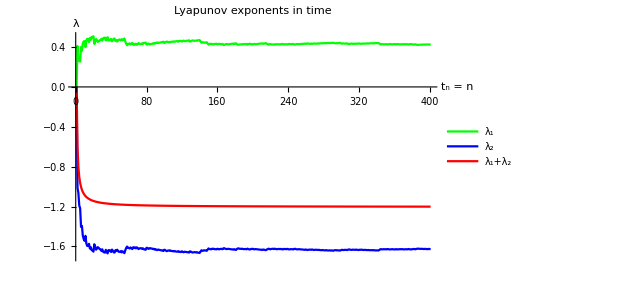

```mathematica
Show[p1,p2,p3,PlotRange->{{0,400},{-1.7,0.5}},PlotLabel->"Lyapunov exponents in time",AxesLabel->{"t_n = n","λ"}]
```

From this plot, it follows that the Lyapunov exponents have converged to a fixed value: λ_1≈ 0.42;  λ_2≈-1.63. 
Also, it’s clear that the sum of the exponents is numerically much more stable than the individual exponents are (less oscillations on the same scale).

#### f)

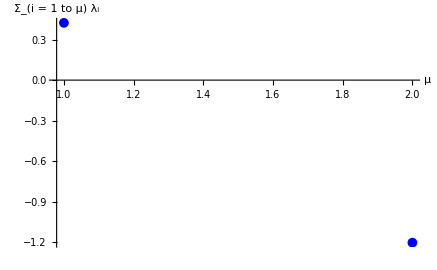

```mathematica
plots = ListPlot[{{1,lam1},{2,lam1+lam2}},AxesLabel->{"μ","Σ_(i  =  1 to μ) λ_i"},PlotMarkers->{Automatic,10},PlotStyle -> {Blue}]
```

To find the Lyapunov dimension D_L, we need to connect the two dots above with a line and look for the intersection with the μ axis.

```mathematica
Lyapline=Fit[{{1,lam1},{2,lam1+lam2}},{1,x},x]
```

2.05241-1.62819 x

```mathematica
plyap = Plot[Lyapline, {x,0,2},PlotStyle->Black,PlotLegends->{"Connecting line"}];
```

```mathematica
Solve[Lyapline ==0,x]
```

{{x→1.26055}}

```mathematica
punt = ListPlot[{{1.2605462259417504,0}},PlotMarkers->{Automatic,10}, PlotStyle -> {Red},PlotLegends->{"Intersection μ axis = D_L"}];
```

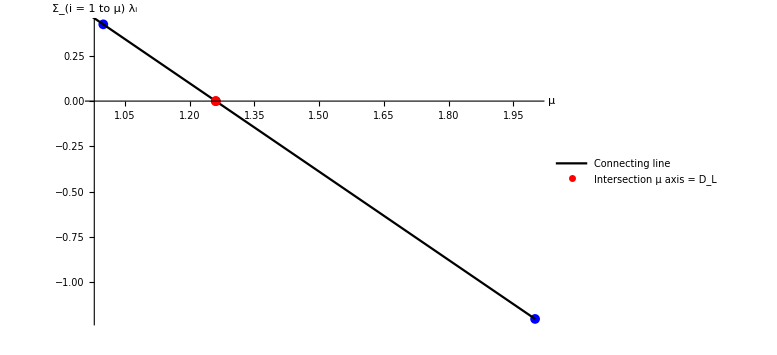

```mathematica
Show[plots,plyap,punt]
```

So from this calculation, it follows that D_L≈ 1.26 which lies quite close to D_1≈ 1.22 which agrees with the Kaplan-Yorke conjecture. 
A better agreement can be obtained by letting the dynamics run for a longer time.